# Geometry: A Primer

```mathematica
WordData["geometry","Definitions"]
```

{{geometry,Noun}→the pure mathematics of points and lines and curves and surfaces}

```mathematica
data:=ExampleData[{"Geometry3D","StanfordBunny"},"VertexData"]
ListSurfacePlot3D[data,MaxPlotPoints->100]
```

-Graphics3D-

```mathematica
-Graphics3D-//FullForm
```

Graphics3D[GraphicsComplex[List[List[-0.0931172,-0.0271478,0.121846],List[-0.0931299,-0.0271077,0.121846],List[-0.0931172,-0.0271077,0.121793],List[-0.0927459,-0.0271077,0.120287],List[-0.0924086,-0.0283266,0.120287],List[-0.0927569,-0.0283266,0.121846],List[-0.0935798,-0.0258888,0.121846],List[-0.0932285,-0.0258888,0.120287],List[-0.0931172,-0.0261679,0.120287],List[-0.0931172,-0.0276992,0.123405],List[-0.0932923,-0.0271077,0.123405],List[-0.0925861,-0.0295456,0.121846],List[-0.0923327,-0.0295456,0.120287],List[-0.0921571,-0.0271077,0.118728],List[-0.0919126,-0.0283266,0.118728],List[-0.0929349,-0.0283266,0.123405],List[-0.093988,-0.0246699,0.121846],List[-0.093663,-0.0246699,0.120287],List[-0.0931172,-0.0258888,0.120002],List[-0.0936974,-0.0258888,0.123405],List[-0.0931172,-0.0277484,0.124964],\[LeftSkeleton]53053\[RightSkeleton],List[0.0237719,0.00886553,0.0426096],List[0.0541364,0.00135501,0.0618539],List[0.0214362,0.0163761,0.0426096],List[0.0477864,-0.013666,0.0426096],List[0.0579541,-0.013666,0.0522317],List[0.0596929,-0.00615552,0.0618539],List[0.052309,0.00135501,0.0522317],List[0.0406485,0.00135501,0.0426096],List[0.0568879,-0.00615552,0.0522317],List[0.0467733,-0.00615552,0.0426096],List[-0.0848545,-0.0286871,0.0907203],List[-0.0753469,-0.0286871,0.071476],List[-0.0464758,-0.0437081,0.0907203],List[-0.0750142,0.0163761,0.148453],List[-0.0465894,-0.0437081,0.0426096],List[-0.0655963,0.0313971,0.167698],List[-0.0255194,0.0238866,0.100342],List[-0.0263759,0.00886553,0.17732],List[0.0221788,0.0238866,0.0907203],List[0.0326284,-0.0286871,0.0426096]],List[List[\[LeftSkeleton]1\[RightSkeleton]],List[\[LeftSkeleton]1\[RightSkeleton]]],Rule[VertexNormals,List[\[LeftSkeleton]1\[RightSkeleton]]]],\[LeftSkeleton]8\[RightSkeleton]]

```mathematica
ListSurfacePlot3D[data,MaxPlotPoints->100,Mesh->50,Axes->None,MeshFunctions->(#1+#2+#3&),MeshShading->{None,Yellow}]
```

-Graphics3D-

## Point of Origin: Exit the Void

```mathematica
point[coords_,size_:.03,plotRange_:1,color_:Blue]:=Graphics[{PointSize[size],color,Point[coords]},Frame->True,Axes->True,PlotRange->plotRange,AxesLabel->{x,y},ImageSize->500]
```

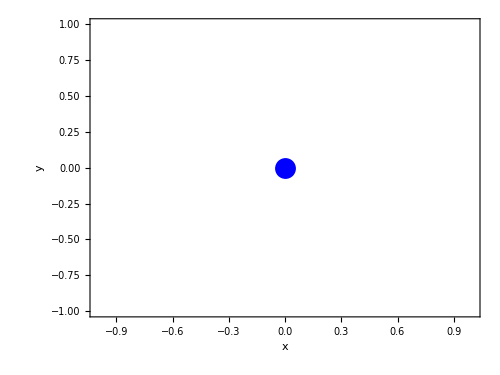

```mathematica
point[{0,0}]
```

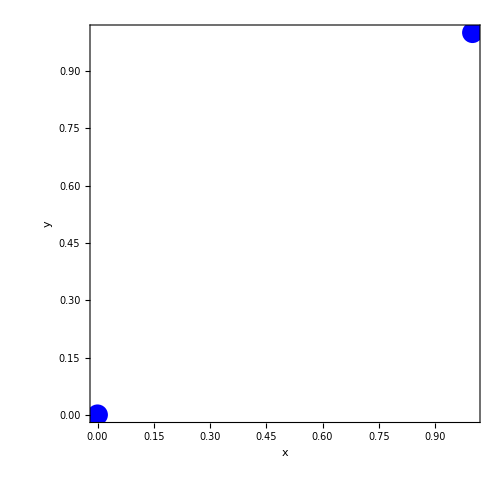

```mathematica
point[{{0,0},{1,1}}]
```

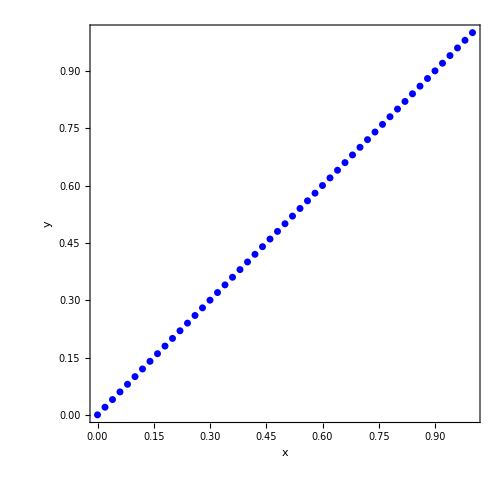

```mathematica
point[Table[{t,t},{t,0,1,1/50}],.01]
```

#### Is this a line?

```mathematica
tenthousandPoints[max_]:=point[Table[{t,t},{t,0,max,1/10000}],.01,max]
Manipulate[tenthousandPoints[max],{max,{1,.1,.01,.001,.0001}}]
```

## The Shortest Distance Between Two Points

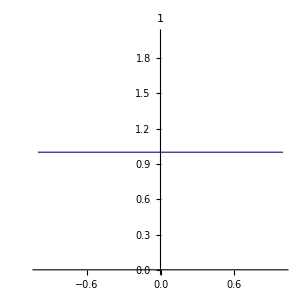
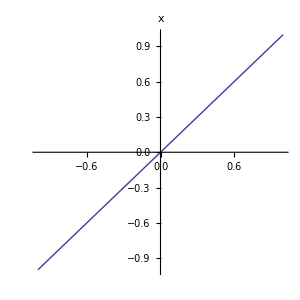
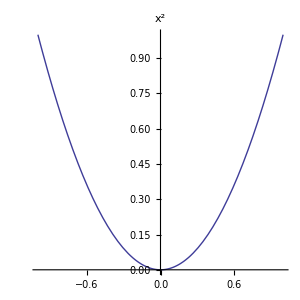
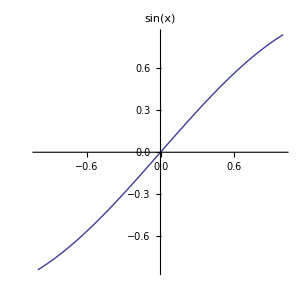
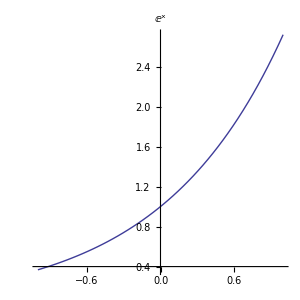

```mathematica
Plot[#,{x,-1,1},AspectRatio->1,ImageSize->300,PlotLabel->Style[#,16]]&/@{1,x,x^2,Sin[x],E^x}
```

### How ‘bout outside linear coordinates?

#### Polar

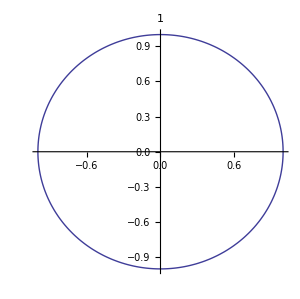
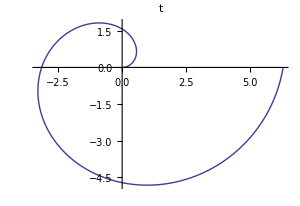
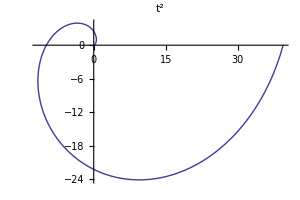
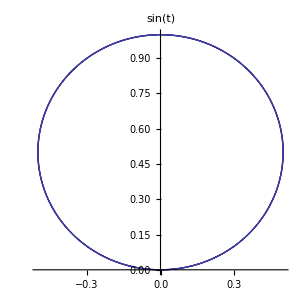
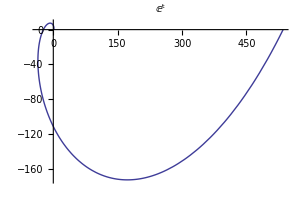

```mathematica
PolarPlot[#,{t,0,2π}, AspectRatio->Automatic,ImageSize->300,PlotLabel->Style[#,16]]&/@{1,t,t^2,Sin[t],E^t}
```

#### Linear X; Logarithmic Y

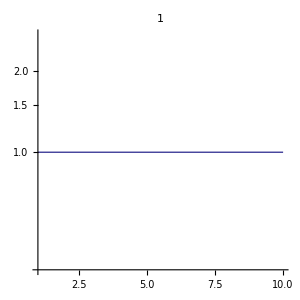
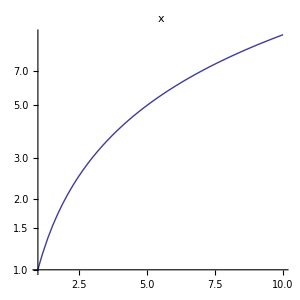
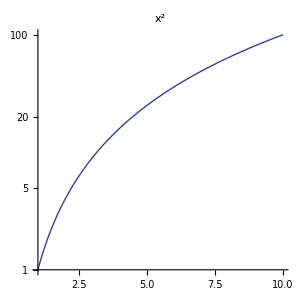
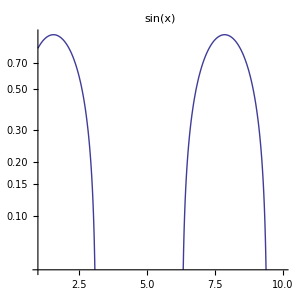
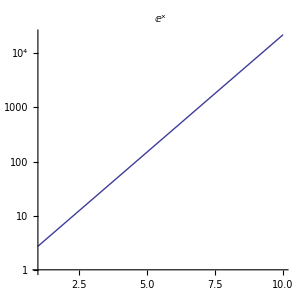

```mathematica
LogPlot[#,{x,1,10}, AspectRatio->1,ImageSize->300,PlotLabel->Style[#,16]]&/@{1,x,x^2,Sin[x],E^x}
```

#### Logarithmic X; Linear Y

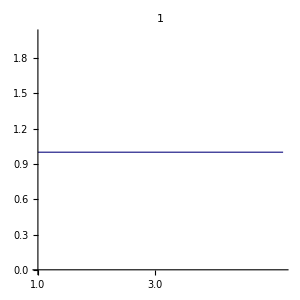
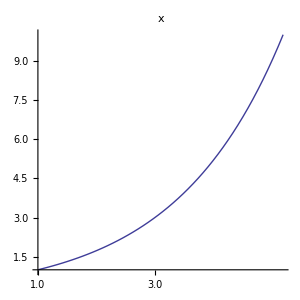
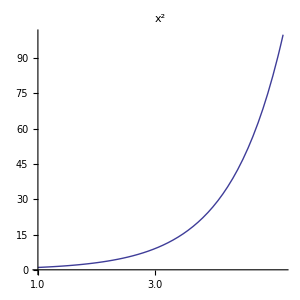
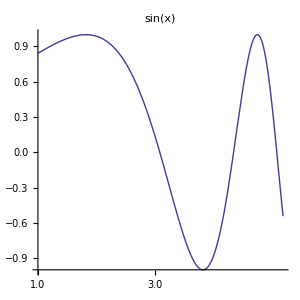
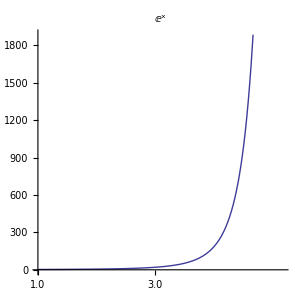

```mathematica
LogLinearPlot[#,{x,1,10}, AspectRatio->1,ImageSize->300,PlotLabel->Style[#,16]]&/@{1,x,x^2,Sin[x],E^x}
```

#### Logarithmic X; Logarithmic Y

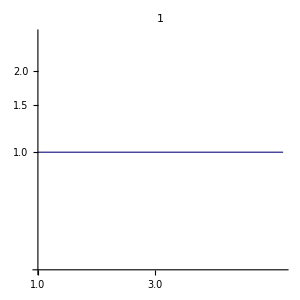
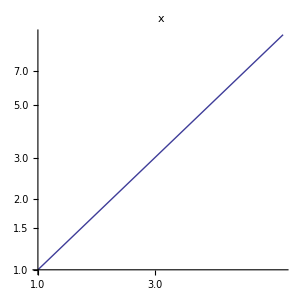
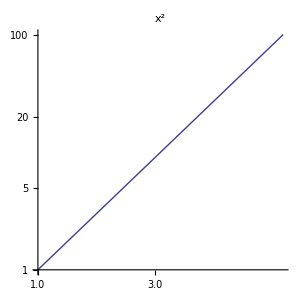
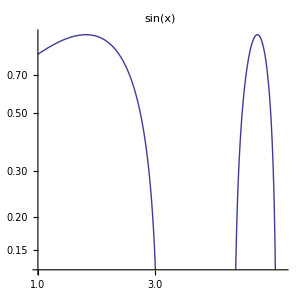
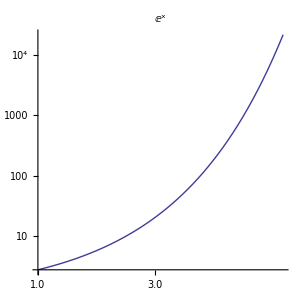

```mathematica
LogLogPlot[#,{x,1,10}, AspectRatio->1,ImageSize->300,PlotLabel->Style[#,16]]&/@{1,x,x^2,Sin[x],E^x}
```

### Quadratic Equation

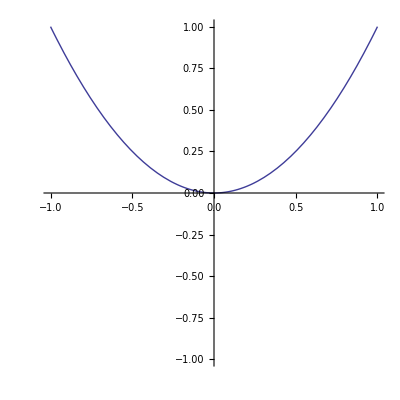

```mathematica
Plot[x^2,{x,-1,1},PlotRange->1,AspectRatio->Automatic]
```

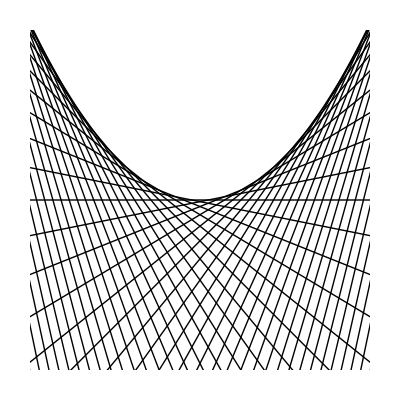

```mathematica
f[x_]:=x^2
p=Table[{{a-2,f'[a]((a-2)-a)+f[a]},{a+2,f'[a]((a+2)-a)+f[a]}},{a,-10,10,.1}];
Graphics[Line[p],PlotRange->{{-1,1},{-1,1}}]
```

### Moiré pattern — Would you believe these are all cartesian lines?

```mathematica
Manipulate[Graphics[Table[Line[{{{x,0},{1-x,1}},{{0,x},{1,1-x}}}],{x,0,1,density}],ImageSize->600],{{density,.01},{1,.5,.25,.1,.05,.025,.01,.005,.0025,.001}}]
```

## Curves

### A circle, or just a high fidelity n-gon? Are they different!?

```mathematica
Manipulate[Graphics[{EdgeForm[Black],LightRed,Polygon[Table[{Cos[2Pi k/n],Sin[2Pi k/n]},{k,n}]]},ImageSize->300],{{n,3},3,100,1}]
```

### Do you polygon?

This looks scary, but focus on the English! We’re manipulating a graphic consisting of a table of colored polygons which are comprised of a bunch of sin+cos values. With rMax starting at 6 and qMax starting at 8, can you figure out what these values do?

```mathematica
With[{d=2Pi/qMax},Manipulate[Graphics[Table[{EdgeForm[Opacity[.6]],Hue[(-11+q+10 r)/(rMax qMax)],Polygon[{(8-r){Cos[d(q-1)],Sin[d(q-1)]},(8-r){Cos[d(q+1)],Sin[d(q+1)]},(10-r){Cos[d q],Sin[d q]}}]},{r,rMax},{q,qMax}]],{{rMax,6},1,40,1},{{qMax,8},1,20,1}]]
```

## Sexy+Lazy Application: The Bézier Curve

#### Demonstration by example; here’s an arbitrary curve

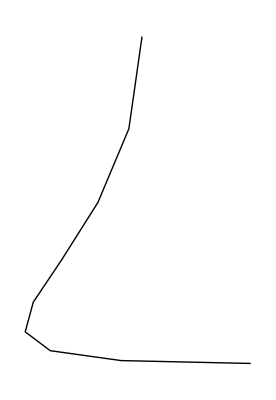

```mathematica
start:={{2,2},{2,-3},{-4,-4},{4,-4}}
Graphics[{BezierCurve[start]}]
```

#### Now let’s write a tweening function—this just transitions linearly over time. In this case, t is arbitrary

```mathematica
tween[p1_,p2_,t_]:=(1-t)p1+t p2
```

```mathematica
Plot3D[(1-t)x+t x,{x,-5,5},{t,-1,1},AxesLabel->Automatic,ImageSize->600]
```

-Graphics3D-

#### Using our tweening function and the starting curve

```mathematica
bezier[c1_,c2_,c3_,c4_,t_]:=Graphics[{Thick,BezierCurve[{c1,c2,c3,c4}],Green,Line[{c1,c2,c3,c4}],Red,Point[{c1,c2,c3,c4}],Thick,BezierCurve[start],Green,Line[start],Red,Point[start],Thickness[.01],Purple,BezierCurve[tween[start,{c1,c2,c3,c4},t]]}]
```

```mathematica
Manipulate[Animate[bezier[c1,c2,c3,c4,t],{t,0,1},AnimationDirection->ForwardBackward],Row[{Control[{c1,{-4,-4},{4,4}}],Control[{c2,{-4,-4},{4,4}}],Control[{c3,{-4,-4},{4,4}}],Control[{c4,{-4,-4},{4,4}}]}],AspectRatio->1]
```

```mathematica
z
```

z

### Bézier Flower

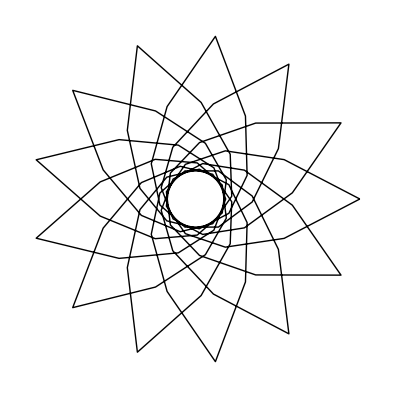

```mathematica
Graphics[BezierCurve[Table[{Cos[2k Pi/13],Sin[2 k Pi/13]},{k,0,156,4}]],ImageSize->600]
```

#### Hmm...the flower has 13 petals, and the divisor inside Cos and Sin is 13; additionally, the max limit of k is 156, incrementing by 4. 156/13 = 12 = 4*3 Any intuitions here?

```mathematica
Manipulate[Graphics[BezierCurve[Table[{Cos[2k Pi/petals],Sin[2 k Pi/petals]},{k,0,3*increment*petals,increment}]],ImageSize->600],{{petals,13},3,28,1},{{increment,4},{2,3,4,5,6}}]
```

## Hyperbolic Spaces | Contour Surfaces

```mathematica
Manipulate[plot[#,{t,-π s,π s},PlotLabel->Style[#,16],PlotStyle->Thick,AspectRatio->1,ImageSize->250,PlotRange->Automatic]&/@{Sinh[x],Sin[x],Cosh[x],Cos[x],Tanh[x],Tan[x],Csch[x],Csc[x],Sech[x],Sec[x],Coth[x],Cot[x]},{{x,t},{1,t,t^2,t^3}},{s,{1,2,4,8,16}},{plot,{Plot,PolarPlot,LogPlot}}]
```

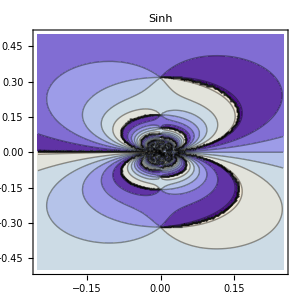
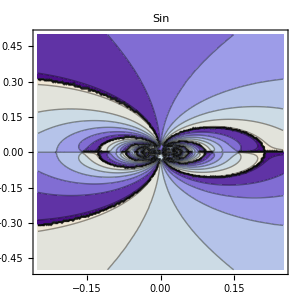
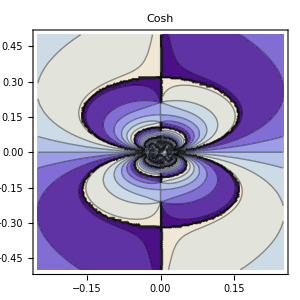
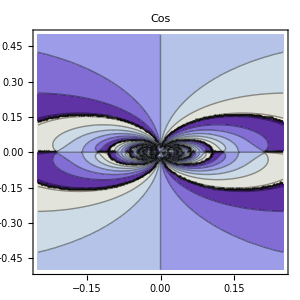
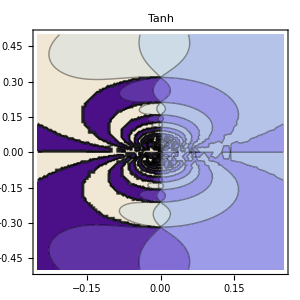
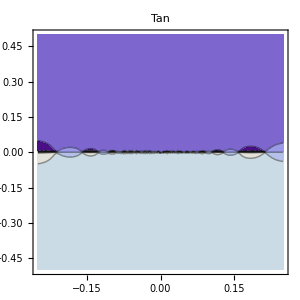
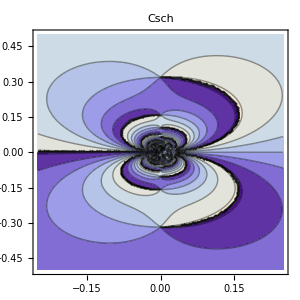
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ContourPlot[Arg[#[1/(x+I y)]],{x,-1/4,1/4},{y,-1/2,1/2},Exclusions->{},PlotRange->All,ImageSize->300,PlotLabel->Style[#,16]]&/@{Sinh,Sin,Cosh,Cos,Tanh,Tan,Csch,Csc,Sech,Sec,Coth,Cot}
```

## Into....the third dimension!

```mathematica
ContourPlot3D[ Cos[x]Sin[y]+Cos[y]Sin[z]+Cos[z]Sin[x]==0,{x,-2π,2π}, {y,-2π,2π},{z,-2π,2π},ContourStyle->Directive[FaceForm[Orange,Red],Specularity[White,30]],Mesh->None]
```

-Graphics3D-

```mathematica
ContourPlot3D[ Cos[x]Tan[y]+Csc[y]Sin[z]+Cot[z]Sec[x]==0,{x,-2π,2π}, {y,-2π,2π},{z,-2π,2π},ContourStyle->Directive[FaceForm[Green,Purple],Specularity[White,30]],Mesh->8,Contours->8]
```

```mathematica
GraphicsGrid[Partition[PolyhedronData/@PolyhedronData[#],7,7,{1,1},{}],ImageSize->600,PlotLabel->#]&/@{"Platonic","UniformDual","Archimedean","Compound","Concave"}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Graphics3D[PolyhedronData[{n,#},"Faces"]&/@{"Laevo","Dextro"},PlotLabel->n,ImageSize->200],{n,{"PentagonalHexecontahedron","PentagonalIcositetrahedron","SnubCube","SnubDodecahedron"}}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

## 2D or Knot-2D

```mathematica
Graphics[Transpose[{{Red,Blue,Green,Red},KnotData["Trefoil", "KnotDiagramData"]}]]
```

-Graphics-

```mathematica
Row[Graphics[KnotData[#,"KnotDiagramData"], Epilog -> Inset[Style[KnotData[#,"AlexanderBriggsNotation"],Large],{Right,Bottom},{Right,Bottom}],ImageSize->200] & /@ Take[KnotData[All],{2,6}]]
```

-Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
Graphics[Transpose[{Table[RGBColor @@ RandomReal[{0,1},3],{Length[#]}], #}]]& @KnotData[{"TorusKnot",{7,30}},"KnotDiagramData"]
```

-Graphics-